## Zentrierte rechteckige Bodenplatte

```mathematica
template=Polygon[{{-w/2,-l/2},{-w/2,l/2},{w/2,l/2},{w/2,-l/2}}]
```

Polygon[{{-w/2,-l/2},{-w/2,l/2},{w/2,l/2},{w/2,-l/2}}]

## 4503

```mathematica
Polygon/@Function[mul,mul #&/@{{-w1/2,l1},{w1/2,l1},{w2/2,l2},{-w2/2,l2}}]/@{{1,1},{1,-1}}/.{w1->6.2,l1->43.7/2,w2->6.0,l2->53.4/2}
```

{Polygon[{{-3.1,21.85},{3.1,21.85},{3.,26.7},{-3.,26.7}}],Polygon[{{-3.1,-21.85},{3.1,-21.85},{3.,-26.7},{-3.,-26.7}}]}

```mathematica
dimensions4503=Flatten[{Polygon/@Function[mul,mul #&/@{{-w1/2,l1},{w1/2,l1},{w2/2,l2},{-w2/2,l2}}]/@{{1,1},{1,-1}}/.{w1->6.2,l1->43.7/2,w2->6.0,l2->53.4/2},Polygon/@Function[mul,mul #&/@{{-w1/2,l1},{w1/2,l1},{w2/2,l2},{-w2/2,l2}}]/@{{1,1},{1,-1}}/.{w1->13.4,l1->75./2,w2->13.2,l2->84./2},Disk[pos,r]/.pos->#&/@{{-w/2,-l/2},{w/2,l/2},{w/2,-l},{-w/2,l}}/.{w->17,l->30,r->2.2/2},Disk[pos,r]/.pos->#&/@{{-w/2,l/2},{w/2,-l/2},{w/2,l},{-w/2,-l}}/.{w->17,l->30,r->3.9/2},Disk[pos,r]/.pos->#&/@{{-w,0},{w,0}}/.{r->2.4/2,w->(9.2+4.0)/2},Disk[pos,r]/.pos->#&/@{{0,0},{0,-l},{0,l}}/.{r->3./2,l->(21+15)/2.},template/.{w->29.0,l->89.6}}]
```

{Polygon[{{-3.1,21.85},{3.1,21.85},{3.,26.7},{-3.,26.7}}],Polygon[{{-3.1,-21.85},{3.1,-21.85},{3.,-26.7},{-3.,-26.7}}],Polygon[{{-6.7,37.5},{6.7,37.5},{6.6,42.},{-6.6,42.}}],Polygon[{{-6.7,-37.5},{6.7,-37.5},{6.6,-42.},{-6.6,-42.}}],Disk[{-17/2,-15},1.1],Disk[{17/2,15},1.1],Disk[{17/2,-30},1.1],Disk[{-17/2,30},1.1],Disk[{-17/2,15},1.95],Disk[{17/2,-15},1.95],Disk[{17/2,30},1.95],Disk[{-17/2,-30},1.95],Disk[{-6.6,0},1.2],Disk[{6.6,0},1.2],Disk[{0,0},1.5],Disk[{0,-18.},1.5],Disk[{0,18.},1.5],Polygon[{{-14.5,-44.8},{-14.5,44.8},{14.5,44.8},{14.5,-44.8}}]}

## 4514

```mathematica
dimensions4514=Flatten[{Disk[pos,r]/.pos->#&/@{{-w/2,l},{w/2,l}}/.{r->3.5/2,w->(18.5+11.5)/2,l->(86.2-78.2)/2},Disk[pos,r]/.pos->#&/@{{-w/2,-l/2},{-w/2,l/2},{w/2,l/2},{w/2,-l/2}}/.{l->(142.+135.)/2,w->(22.4+15.6)/2,r->3.5/2},template/.{w->29.9,l->168.2}}]
```

{Disk[{-7.5,4.},1.75],Disk[{7.5,4.},1.75],Disk[{-9.5,-69.25},1.75],Disk[{-9.5,69.25},1.75],Disk[{9.5,69.25},1.75],Disk[{9.5,-69.25},1.75],Polygon[{{-14.95,-84.1},{-14.95,84.1},{14.95,84.1},{14.95,-84.1}}]}

## Visualisierung

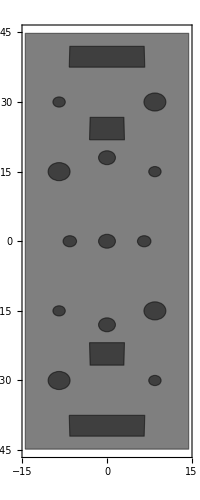

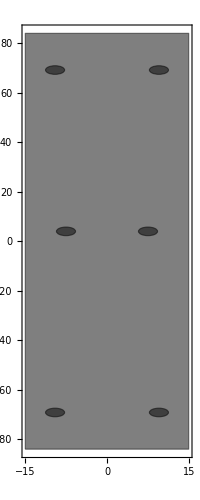

{Null,Null}

```mathematica
Print[Show[Graphics[{Thick,EdgeForm[Thick],Transparent,Opacity[0.5],#},Frame->True]]]&/@{dimensions4503,dimensions4514}
```